# Constrain the lognormal mass function of Primordial black holes (PBH) using LIGO’s events

## Setup

Model name

```mathematica
model="lognormal-PBH-Liu-O1O2";
```

Launch Kernels

```mathematica
cpuCores=8; (* Specify how many cpu cores to use *)
LaunchKernels[cpuCores];
Off[NIntegrate::slwcon];
ParallelEvaluate[Off[NIntegrate::slwcon]];
```

Set the directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Off[Power::infy,Infinity::indet,NDSolve::nlnum,NIntegrate::slwcon];
(*
Needs["NumericalCalculus`"];
Off[General::obspkg,NIntegrate::inumr,NIntegrate::ncvb,NIntegrate::inumri ,NIntegrate::izero];
$TextStyle={FontFamily->"Times",FontSize->7};
*)
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Plot options

```mathematica
plotOptions=Sequence[FrameStyle->(FontFamily->"Times"),BaseStyle->FontSize->18,LabelStyle->Black,Frame->True,Axes->False,PlotRangePadding->None,ImageSize->500,AspectRatio->1];
dx2={1/2,4/2};
contourPlotOptions=Sequence[PlotRange->All,ContourShading->{White,LightRed,Red}];
```

Grid plots for marginalized posteriors

```mathematica
emptyGraph=Graphics[White];
```

```mathematica
(*Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w- sidePadding-1)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
heights=(h- sidePadding-1)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],1},{If[j==1,sidePadding,0],1}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]*)

Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w- 4/5*sidePadding-1)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+4/5*sidePadding;
heights=(h- sidePadding-1)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,4/5*sidePadding,0],1},{If[j==1,sidePadding,0],1}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Data

Read LIGO data

## Mass data

There are 12 data points in total.

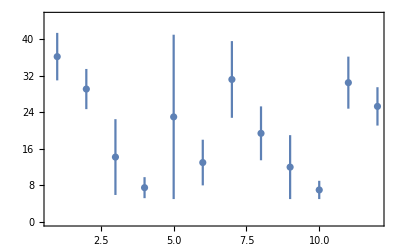

```mathematica
data=ReadList["./LIGO-data/LIGO.txt",{Word,Number,Number,Number,Number,Number,Number}];
nBinary=Length@data;
nobs=2*nBinary;(* N observation *)
Print["There are ",nobs," data points in total."]
Do[name[i]=data[[Ceiling[i/2],1]],{i,1,nobs}];
Do[If[i//OddQ,m[i]=data[[Ceiling[i/2],2]],m[i]=data[[i/2,5]]],{i,1,nobs}];
Do[
If[i//OddQ,
σ[i]=Max[data[[Ceiling[i/2],3]],data[[Ceiling[i/2],4]]],
σ[i]=Max[data[[i/2,6]],data[[i/2,7]]]
],{i,1,nobs}];
plscp=ErrorListPlot[
Table[{m[i],σ[i]},{i,1,nobs}],
Frame->True,
Axes->False,
PlotRange->{All,{0,45}}
]
```

```mathematica
Print["There are ",nBinary," binaries in total."]
binary=Table[Null,nBinary];
For[i=1,i≤nBinary,i++,binary[[i]]={data[[i,2]],Min[data[[i,3]],data[[i,4]]],data[[i,5]],Min[data[[i,6]],data[[i,7]]]}]
binary
```

There are 6 binaries in total.

{{36.2,3.8,29.1,3.7},{14.2,3.7,7.5,2.3},{23,6,13,4},{31.2,6.,19.4,5.3},{12,2,7,2},{30.5,3.,25.3,2.8}}

## Posteriors

### O1 data

```mathematica
eventnames={"GW150914","GW151226","LVT151012"};
Clear[pdm1m2,data,𝒟,i,pdftmp];
pdftmp={};
data[i_?NumberQ]:=ReadList["./LIGO-data/"<>eventnames[[i]]<>"_posterior.txt",{Number,Number}];
𝒟[i_?NumberQ]:=SmoothKernelDistribution[data[i]]

For[i=1,i<=Length@eventnames,i++,
AppendTo[pdftmp,PDF[𝒟[i],{m1,m2}]]
]
(*
For[i=1,i<=3,i++,pdf[i,m1_,m2_]=pdftmp[[i]]]
*)
For[i=1,i<=3,i++,pdm1m2[i,m1_,m2_]=PDF[EstimatedDistribution[data[i],BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ]],{m1,m2}]]
```

```mathematica
Plot3D[pdm1m2[1,m1,m2],{m1,25,53},{m2,20,38},PlotRange->All,PlotPoints->40]
Plot3D[pdm1m2[2,m1,m2],{m1,5,30},{m2,5,12},PlotRange->All,PlotPoints->40]
Plot3D[pdm1m2[3,m1,m2],{m1,5,40},{m2,5,30},PlotRange->All,PlotPoints->40]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Data beyond O1

```mathematica
If[nBinary≥4,
For[i=4,i≤nBinary,i++,
pdm1m2[i,m1_,m2_]=PDF[BinormalDistribution[{binary[[i,1]],binary[[i,3]]},{binary[[i,2]],binary[[i,4]]},0],{m1,m2}]
]
]

i=4;
Plot3D[pdm1m2[i,m1,m2],{m1,8,53},{m2,5,38},PlotRange->All,PlotPoints->40]
NIntegrate[pdm1m2[i,m1,m2],{m1,5,95},{m2,5,95},PrecisionGoal->3]
```

-Graphics3D-

0.996589

LIGO’s Volume Sensitivity

## VT- interpolation

```mathematica
Clear@VTInter;
VTDataList=ReadList["./Backup/VT_1yr_LIGO_O1.txt",{Number,Number,Number}];
LIGOObservationTimeO1=46.1;(* days or 48.6 days *)
LIGOObservationTimeO2=117;(* days *)
LIGOObservationTimeO1AndO2=LIGOObservationTimeO1+LIGOObservationTimeO2;
timeFraction=LIGOObservationTimeO1AndO2/365;
VT1year=Interpolation@VTDataList;
VTInter[m1_,m2_]:=timeFraction*VT1year[m1,m2]
```

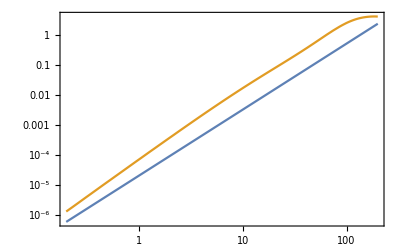

```mathematica
LogLogPlot[{m^2.2/(5*10^4),VTInter[m/2,m/2]},{m,0.20,200},Frame->True]
```

## Merger rate

Original PDF function

{4.77387×10^-15,0.0000250765,0.0529168,0.0000448591,1.5277×10^-14}

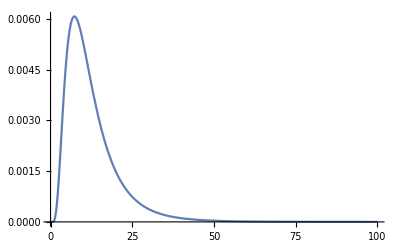

```mathematica
Clear[min,max,Plog];
mMin=3;
mTotMax=150;
mMax=mTotMax-mMin;
Evaluate[min/@{"logf","logmc","σc","logR"}]={-4,0,0.1,-1};
Evaluate[max/@{"logf","logmc","σc","logR"}]={-1,3,3,3};
{min["mc"],max["mc"]}={10^min["logmc"],10^max["logmc"]};
{min["R"],max["R"]}={10^min["logR"],10^max["logR"]};
{logf0,logmc0,mc0,σc0}={-3,Log10@15.,15,0.6};
Plog[i_,mc_,σc_]:=1/(√(2*π)*σc*i)*ⅇ^(-(Log[i/mc])^2/(2*σc^2));
Table[Plog[10^i,mc0,σc0],{i,-1,3}]
Plot[Plog[i,mc0,σc0]/i,{i,10^-4,10^2},PlotRange->All]
```

```mathematica
Integrate[Plog[ii,mc,σc],{ii,0,∞},Assumptions->mc>1&&σc>0]
```

1

```mathematica
1/Integrate[Plog[ii,mc,σc]/ii,{ii,0,∞},Assumptions->mc>1&&σc>0]
```

ⅇ^(-σc^2/2) mc

Binary PDF function

```mathematica
Clear[mpbh,F];
mpbh[mc_,σc_]:=ⅇ^(-σc^2/2) mc
F[i_,mc_,σc_]:=Plog[i,mc,σc]*mpbh[mc,σc]/i;
F[ii,mc,σc]
Integrate[F[ii,mc,σc],{ii,0,∞},Assumptions->mc>1&&σc>0]
```

(ⅇ^(-σc^2/2-Log[ii/mc]^2/(2 σc^2)) mc)/(ii^2 √(2 π) σc)

1

```mathematica
Integrate[l^(-21/37)F[l,mc,σc],{l,0,∞},Assumptions->mc>1&&σc>0]
```

(ⅇ^((1995 σc^2)/2738))/mc^(21/37)

```mathematica
logf0=0.0025693801260000975;
f0=0.0025693801260000975;
logmc0=0.9492306854620738;
mc0=8.896735628637506;
σc0=0.9108320383237213;
{m10,m20}={10,30};
```

```mathematica
1.32*10^6*(f/mpbh[mc,σc])^(53/37)(ⅇ^((1995 σc^2)/2738))/mc^(21/37)F[i,mc,σc]*F[j,mc,σc]*(i*j)^(3/37)*(i+j)^(36/37)
```

(210085. ⅇ^(-(743 σc^2)/2738-Log[i/mc]^2/(2 σc^2)-Log[j/mc]^2/(2 σc^2)) (i j)^(3/37) (i+j)^(36/37) ((ⅇ^(σc^2/2) f)/mc)^(53/37) mc^(53/37))/(i^2 j^2 σc^2)

```mathematica
1.32*10^6*(f/mpbh[mc,σc])^(53/37)(ⅇ^((1995 σc^2)/2738))/mc^(21/37)F[i,mc,σc]*F[j,mc,σc]*(i*j)^(3/37)*(i+j)^(36/37)//FullSimplify
```

(210085. ⅇ^(-(743 σc^4+1369 Log[i/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) (i j)^(3/37) (i+j)^(36/37) ((ⅇ^(σc^2/2) f)/mc)^(53/37) mc^(53/37))/(i^2 j^2 σc^2)

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,mc_,σc_]:=1/(i^2 j^2 σc^2)210084.52488130186 ⅇ^(-(743 σc^4+1369 Log[i/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) (i j)^(3/37) (i+j)^(36/37) ((ⅇ^(σc^2/2) f)/mc)^(53/37) mc^(53/37);
mergerRateDensity1st[f0,m10,m20,mc0,σc0]
```

0.00138437

```mathematica
(*Clear[normalFactorMergerRateDensity1st,normalizedMergerRateDensity1st];
normalFactorMergerRateDensity1st[f_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=NIntegrate[mergerRateDensity1st[f,m1,m2,mc,σc],{m1,0,∞},{m2,0,∞},PrecisionGoal->3];

normalizedMergerRateDensity1st[f_,i_,j_,α_,M_]:=mergerRateDensity1st[f,i,j,α,M]/normalFactorMergerRateDensity1st[f,α,M];
normalFactorMergerRateDensity1st[f0,mc0,σc0]
normalizedMergerRateDensity1st[f0,m10,m20,mc0,σc0]
NIntegrate[normalizedMergerRateDensity1st[f0,m1,m2,mc0,σc0],{m1,0,∞},{m2,0,∞},PrecisionGoal->3]*)
```

```mathematica
mergerRateDensity2nd00[f_,i_,j_,k_,l_,mc_,σc_]:=1.59*10^4*(f/mpbh[mc,σc])^(69/37)k^(6/37)l^(-42/37)(i+j)^(6/37)(i+j+k)^(72/37)F[i,mc,σc]*F[j,mc,σc]*F[k,mc,σc]*F[l,mc,σc]

mergerRateDensity2nd00[f,i,j,k,l,mc,σc]
```

(402.752 ⅇ^(-2 σc^2-Log[i/mc]^2/(2 σc^2)-Log[j/mc]^2/(2 σc^2)-Log[k/mc]^2/(2 σc^2)-Log[l/mc]^2/(2 σc^2)) (i+j)^(6/37) (i+j+k)^(72/37) ((ⅇ^(σc^2/2) f)/mc)^(69/37) mc^4)/(i^2 j^2 k^(68/37) l^(116/37) σc^4)

```mathematica
Integrate[mergerRateDensity2nd00[f,i-e,e,j,l,mc,σc],{l,0,∞},Assumptions->mc>1&&σc>0]
```

(1009.55 ⅇ^(-(-3318 σc^4+1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) f^(69/37) i^(6/37) (i+j)^(72/37))/(e^2 (-1. e+i)^2 j^(68/37) σc^3)

```mathematica
mergerRateDensity2nd0[f_?NumericQ,i_?NumericQ,j_?NumericQ,e_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=(1009.5488113544313 ⅇ^(-(-3318 σc^4+1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) f^(69/37) i^(6/37) (i+j)^(72/37))/(e^2 (-1. e+i)^2 j^(68/37) σc^3)
```

```mathematica
e0=0.5;
mergerRateDensity2nd0[f0,m10,m20,e0,mc0,σc0]
```

2.80198×10^-6

```mathematica
mergerRateDensity2nd1[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=(1009.5488113544313  f^(69/37)i^(6/37) (i+j)^(72/37))/(j^(68/37) σc^3)ⅇ^(-(-3318 σc^4+1369 Log[j/mc]^2)/(2738 σc^2))NIntegrate[(ⅇ^(-(1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2)/(2738 σc^2)))/(e^2 (-1. e+i)^2),{e,0,i},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
mergerRateDensity2nd1[f0,m10,m20,mc0,σc0]//Timing
```

{0.00083,0.000716225}

```mathematica
mergerRateDensity2nd[f0,m10,m20,mc0,σc0]//Timing
```

{0.001319,0.000939191}

```mathematica
Clear[mergerRateDensity2nd];
mergerRateDensity2nd[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=1/2(mergerRateDensity2nd1[f,i,j,mc,σc]+mergerRateDensity2nd1[f,j,i,mc,σc])
```

```mathematica
Clear@mergerRateDensity;
mergerRateDensity[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=If[i≥j,mergerRateDensity1st[f,i,j,mc,σc]+mergerRateDensity2nd[f,i,j,mc,σc],mergerRateDensity[f,j,i,mc,σc]];

mergerRateDensity[f0,m10,m20,mc0,σc0]//AbsoluteTiming
NIntegrate[mergerRateDensity[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{0.001188,0.0195009}

{0.629888,91.6231}

```mathematica
Clear@R0;
R0[f_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=R0[f,mc,σc]=NIntegrate[mergerRateDensity[f,m1,m2,mc,σc],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R0[f0,mc0,σc0]//AbsoluteTiming
```

{0.633823,91.6231}

```mathematica
mergerRateDensity1st[f0,m10,m20,mc0,σc0]
```

0.00138437

```mathematica
mergerRateDensity2nd[f0,m10,m20,mc0,σc0]
```

0.000140577

```mathematica
5^3*10/60/6.
```

3.47222

```mathematica
step[para_,nSteps_:20]:=(max[para]-min[para])/nSteps
step["logf"]

min["m1"]=mMin;
max["m1"]=mMax;
min["m2"]=mMin;
max["m2"]=mMax;
```

3/20

```mathematica
(* only need to evaluate once *)

(*(RData=ParallelTable[
{{logf,m1,m2,logmc,σc},mergerRateDensity[10^logf,m1,m2,10^logmc,σc]},
{logf,min["logf"],max["logf"],step["logf"]},
{m1,min["m1"],max["m1"],step["m1"]},
{m2,min["m2"],max["m2"],step["m2"]},
{logmc,min["logmc"],max["logmc"],step["logmc"]},
{σc,min["σc"],max["σc"],step["σc"]}];
)//AbsoluteTiming
Flatten[RData,4]//Length
Export[".//backups//"<>model<>"_RData"<>".m",Flatten[RData,4]];*)
```

```mathematica
(*RInter=Interpolation@Import[".//backups//"<>model<>"_RData"<>".m"]*)
(*Plot3D[RInter[logf0,m10,m20,logmc,σc],{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PlotRange->All]*)
```

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=mergerRateDensity2nd[f,i,j,mc,σc]/mergerRateDensity1st[f,i,j,mc,σc];
```

```mathematica
R1=NIntegrate[mergerRateDensity1st[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R2=NIntegrate[mergerRateDensity2nd[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

R2/R1
```

49.1292

1.49723

0.0304753

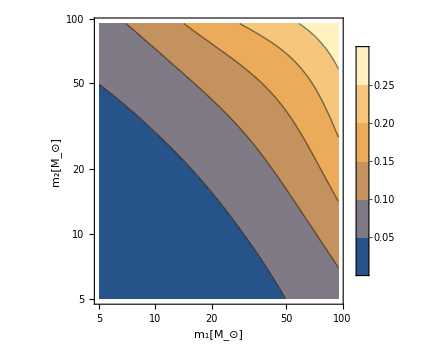

```mathematica
ContourPlot[ratioR[f0,i,j,mc0,σc0],{i,mMin,mMax},{j,mMin,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-log.pdf",%]*)
```

```mathematica
Plot3D[mergerRateDensity1st[f0,i,j,mc0,σc0],{i,mMin,mMax},{j,mMin,mMax},PlotLegends->Automatic]
```

-Graphics3D-

## Likelihood

Normalization factor

```mathematica
Clear@βR0;
βR0[logf_?NumericQ,logmc_?NumericQ,σc_?NumericQ]:=βR0[logf,logmc,σc]=NIntegrate[mergerRateDensity[10^logf,m1,m2,10^logmc,σc]*VTInter[m1,m2],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
βR0[logf0,logmc0,σc0]//AbsoluteTiming
```

{0.327751,2.77487}

```mathematica
NIntegrate[(mergerRateDensity2nd0[f0,m1,m2,e,mc0,σc0])*VTInter[m1,m2],{m1,mMin,mMax},{m2,mMin,mMax},{e,0,m1},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

$Aborted

## βInter - Interpolation of β

```mathematica
(* only need to evaluate once *)

(*(βR0Data=ParallelTable[{{logf,logmc,σc},βR0[logf,logmc,σc]},{logf,min["logf"],max["logf"],logfStep},{logmc,min["logmc"],max["logmc"],logmcStep},{σc,min["σc"],max["σc"],σcStep}];)//AbsoluteTiming
Flatten[βR0Data,2]//Length
Export[".//backups//"<>model<>"_βR0Data"<>".m",Flatten[βR0Data,2]];*)
```

```mathematica
βR0Inter=Interpolation@Import[".//backups//"<>model<>"_βR0Data"<>".m"]
Plot3D[βR0Inter[logf0,logmc,σc],{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

```mathematica
ⅇ^(-βR0Inter[logf0,logmc0,σc0])
```

0.0623573

```mathematica
Plot3D[ⅇ^(-βR0Inter[logf0,logmc,σc]),{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]}]
```

-Graphics3D-

Likelihood for one event

```mathematica
Clear@pdα;
pdα[i_?IntegerQ,f_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=NIntegrate[pdm1m2[i,m1,m2]*mergerRateDensity[f,m1,m2,mc,σc],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
pdα[1,f0,mc0,σc0]//AbsoluteTiming
```

{1.13254,0.0201374}

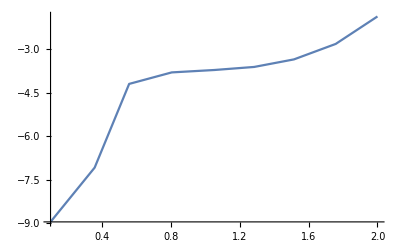
{65.5662,-Graphics-}

```mathematica
Plot[Log@pdα[1,f0,mc0,σc],{σc,0.1,2},PlotPoints->5,MaxRecursion->1]//AbsoluteTiming
```

pdαSumInter - Interpolation of pdαSum

```mathematica
Clear@pdαSum;
pdαSum[logf_?NumericQ,logmc_?NumericQ,σc_?NumericQ]:=pdαSum[logf,logmc,σc]=Sum[Log@pdα[i,10^logf,10^logmc,σc],{i,nBinary}]
pdαSum[logf0,logmc0,σc0]//AbsoluteTiming
```

{8.36554,-29.8024}

```mathematica
(* only need to evaluate once *)
(*
(pdαSumData=ParallelTable[{{logf,logmc,σc},pdαSum[logf,logmc,σc]},{logf,min["logf"],max["logf"],logfStep},{logmc,min["logmc"],max["logmc"],logmcStep},{σc,min["σc"],max["σc"],σcStep}];)//AbsoluteTiming
Flatten[pdαSumData,2]//Length
Export[".//backups//"<>model<>"_pdαSumData"<>".m",Flatten[pdαSumData,2]];*)
```

```mathematica
pdSumInter=Interpolation@Import[".//backups//"<>model<>"_pdαSumData"<>".m"]
Plot3D[pdSumInter[logf0,logmc,σc],{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

## Posteriors

```mathematica
postNorm=NIntegrate[10^logf*10^logmc*ⅇ^(-βR0Inter[logf,logmc,σc])*ⅇ^pdSumInter[logf,logmc,σc],{logf,min["logf"],max["logf"]},{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

6.53283×10^-17

```mathematica
Clear@post;
post[logf_?NumericQ,logmc_?NumericQ,σc_?NumericQ]:=post[logf,logmc,σc]=1/postNorm 10^logf*10^logmc*ⅇ^(-βR0Inter[logf,logmc,σc])*ⅇ^pdSumInter[logf,logmc,σc]

post[logf0,logmc0,σc0]//AbsoluteTiming

NIntegrate[post[logf,logmc,σc],{logf,min["logf"],max["logf"]},{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

{0.000112,1.80908}

1.

## Contour plots

1D Marginalized posteriors

## Credible intervals

```mathematica
Clear[cdf,lower,upper,median];
cdf[para_?StringQ,y_?NumericQ]:=NIntegrate[marginalPosterior1D[para,x],{x,min[para],y},PrecisionGoal->3];lower[para_?StringQ]:=lower[para]=x/.FindRoot[cdf[para,x]==0.05,{x,min[para],max[para]},PrecisionGoal->3];
upper[para_?StringQ]:=upper[para]=x/.FindRoot[cdf[para,x]==0.95,{x,min[para],max[para]},PrecisionGoal->3];
median[para_?StringQ]:=median[para]=x/.FindRoot[cdf[para,x]==0.5,{x,min[para],max[para]},PrecisionGoal->3];

minus[x_?StringQ]:=lower[x]-median[x];
plus[x_?StringQ]:=upper[x]-median[x];
range[x_?StringQ]:={lower[x],median[x],upper[x],plus[x],minus[x]}
```

## logf parameter

```mathematica
NIntegrate[post[logf,logmc,σc],{logf,min["logf"],max["logf"]},{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

1.

```mathematica
marginalPosterior1D["logf",logf_?NumericQ]:=marginalPosterior1D["logf",logf]=NIntegrate[post[logf,logmc,σc],{logmc,min["logmc"],max["logmc"]},{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]


NIntegrate[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{0.001328,0.999724}

```mathematica
range["logf"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logf",range["logf"][[ii]]],{ii,3}]
```

{0.081873,{-2.91987,-2.59017,-2.02836,0.561808,-0.329698}}

{0.00120263,0.00256938,0.00936777,3.64592,0.468061}

{0.05,0.5,0.95}

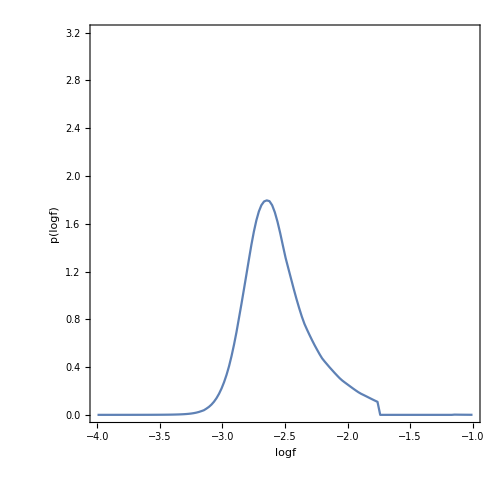

```mathematica
plot1D["logf"]=Plot[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PlotRange->{All,{0.0,3.2}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->4,FrameLabel -> {"logf", "p(logf)"}]
```

## mc parameter

```mathematica
marginalPosterior1D["logmc",logmc_?NumericQ]:=marginalPosterior1D["logmc",logmc]=NIntegrate[post[logf,logmc,σc],{logf,min["logf"],max["logf"]},{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
marginalPosterior1D["logmc",logmc0]//AbsoluteTiming

NIntegrate[marginalPosterior1D["logmc",logmc],{logmc,min["logmc"],max["logmc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{4.×10^-6,1.66126}

{0.001481,1.01477}

```mathematica
range["logmc"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logmc",range["logmc"][[ii]]],{ii,3}]
```

{0.081442,{0.201032,0.949231,1.22344,0.274208,-0.748199}}

{1.58866,8.89674,16.7278,1.88022,0.178567}

{0.05,0.5,0.95}

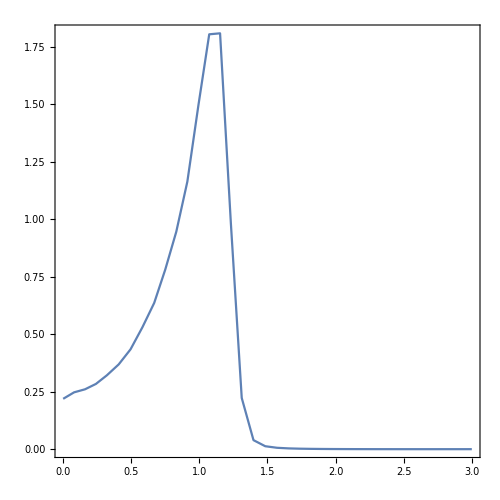

```mathematica
plot1D["logmc"]=Plot[marginalPosterior1D["logmc",logmc],{logmc,min["logmc"],max["logmc"]},PlotRange->All,Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2]
```

## σc parameter

```mathematica
marginalPosterior1D["σc",σc_?NumericQ]:=marginalPosterior1D["σc",σc]=NIntegrate[post[logf,logmc,σc],{logf,min["logf"],max["logf"]},{logmc,min["logmc"],max["logmc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

NIntegrate[marginalPosterior1D["σc",σc],{σc,min["σc"],max["σc"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{0.001454,1.02005}

```mathematica
range["σc"]//AbsoluteTiming
Table[cdf["σc",range["σc"][[ii]]],{ii,3}]
```

{0.079377,{0.490513,0.910832,1.41475,0.503922,-0.420319}}

{0.05,0.5,0.95}

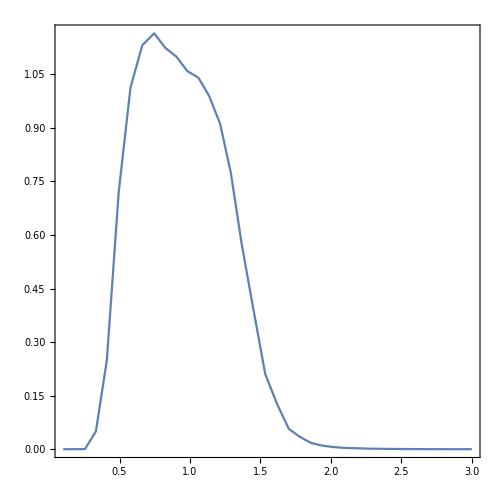

```mathematica
plot1D["σc"]=Plot[marginalPosterior1D["σc",σc],{σc,min["σc"],max["σc"]},PlotRange->All,Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2]
```

## R parameter

```mathematica
{10^median["logf"],10^median["logmc"],median["σc"]}
```

{0.00256938,8.89674,0.910832}

```mathematica
R0Fit=R0[10^median["logf"],10^median["logmc"],median["σc"]]
```

50.6264

```mathematica
βR0Inter[median["logf"],median["logmc"],median["σc"]]
```

6.15416

```mathematica
R0Post[R0_]:=R0^nBinary*ⅇ^(-R0 βR0Inter[median["logf"],median["logmc"],median["σc"]]/R0Fit)
```

```mathematica
NIntegrate[R0Post[R],{R,min["R"],max["R"]}]
```

1.83566×10^9

```mathematica
normR=NIntegrate[R0Post[R],{R,min["R"],max["R"]}];
marginalPosterior1D["R",R_?NumericQ]:=R0Post[R]/normR;

NIntegrate[marginalPosterior1D["R",R],{R,min["R"],max["R"]}]
```

1.

```mathematica
range["R"]//AbsoluteTiming
```

{0.105332,{27.0262,54.8669,97.42,42.5531,-27.8407}}

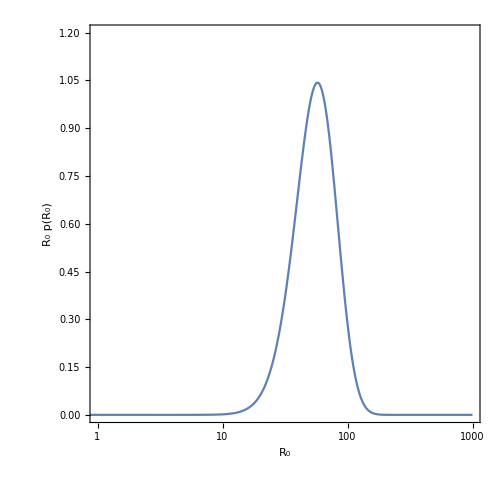

```mathematica
p2=LogLinearPlot[R*marginalPosterior1D["R",R],{R,min["R"],max["R"]},Evaluate@plotOptions,FrameLabel -> {"R_0", "R_0 p(R_0)"},PlotRange->{{1,10^3},{0,1.2}},FrameTicks->{{None,None},{True,None}}]
```

2D Marginalized posteriors

```mathematica
Clear[posteriorFit,marginalPosterior2D,marginalPosterior2DPlot];
posteriorFit[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2]=FindMaximum[marginalPosterior2D[para1,para2,x1,x2],{x1,median[para1],min[para1],max[para1]},{x2,median[para2],min[para2],max[para2]},PrecisionGoal->3]

constours[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2][[1]]*ⅇ^-dx2;
marginalPosterior2DPlot[para1_?StringQ,para2_?StringQ,opts:OptionsPattern[]]:=ContourPlot[marginalPosterior2D[para1,para2,x1,x2],{x1,min[para1]+0.05,max[para1]-0.1},{x2,min[para2],max[para2]},Contours->constours[para1,para2],Evaluate[contourPlotOptions,plotOptions],opts]
```

## logmc-σc

```mathematica
marginalPosterior2D["logmc","σc",logmc_?NumericQ,σc_?NumericQ]:=marginalPosterior2D["logmc","σc",logmc,σc]=NIntegrate[post[logf,logmc,σc],{logf,min["logf"],max["logf"]},PrecisionGoal->3]

marginalPosterior2D["logmc","σc",logmc0,σc0]
```

4.21689

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.9852,{x1→1.12987,x2→0.59229}}

NIntegrate::inumri: The integrand post[logf,0.0500582,0.100059] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-4,-1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

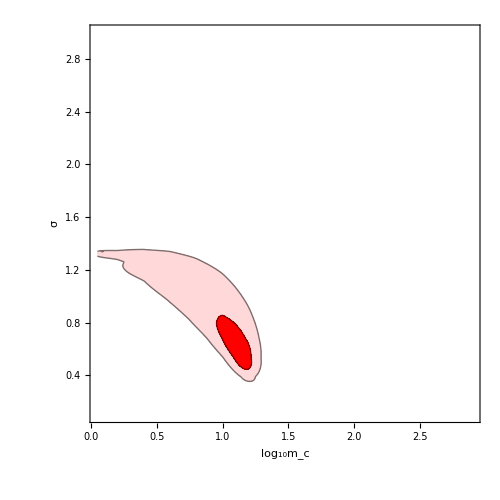

```mathematica
posteriorFit["logmc","σc"]

p1=plot2D["logmc","σc"]=marginalPosterior2DPlot["logmc","σc",PlotPoints->50,MaxRecursion->2,FrameLabel -> {"log_10m_c", "σ"},FrameTicks->{{True,None},{True,True}}]
```

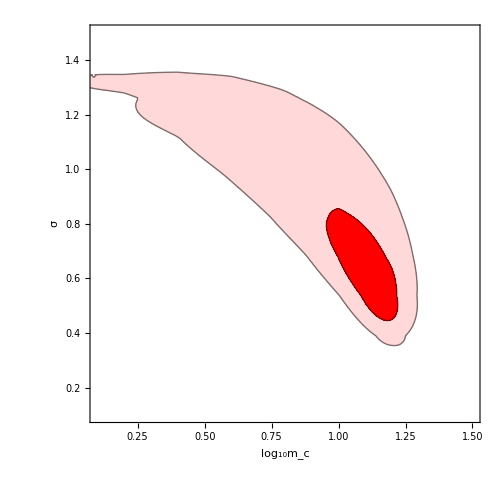

```mathematica
p3=Show[p1,PlotRange->{{0.1,1.5},{0.1,1.5}},FrameTicks->{{True,True},{True,True}}]
```

## Results

```mathematica
p1=-Graphics-;
```

```mathematica
p20=-Graphics-;
```

```mathematica
plotOptions0=Sequence[FrameStyle->(FontFamily->"Times"),BaseStyle->FontSize->25,LabelStyle->Black,Frame->True,Axes->False,PlotRangePadding->None,ImageSize->500,AspectRatio->1];
```

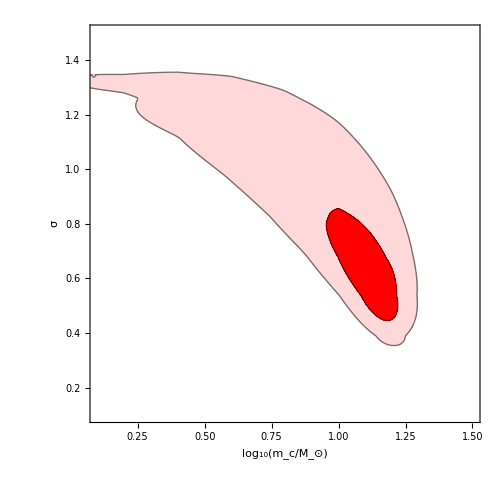

```mathematica
p3=Show[p1,PlotRange->{{0.1,1.5},{0.1,1.5}},FrameTicks->{{True,True},{True,True}},Evaluate@plotOptions0,FrameLabel->{"log_10(m_c/M_⊙)","σ"}]
```

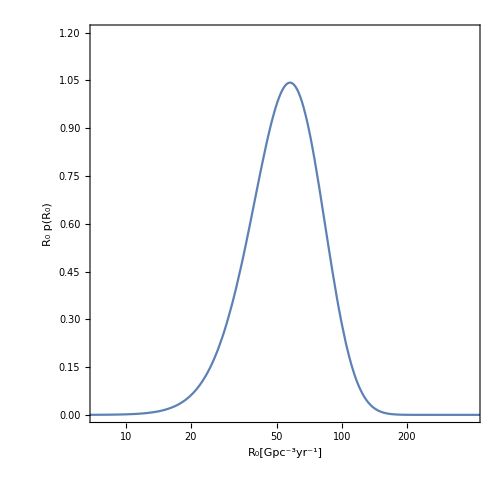

```mathematica
p2=Show[p20,Evaluate@plotOptions0,PlotRange->{{2,6},{0,1.2}},FrameLabel-> {"R_0[Gpc^-3yr^-1]", "R_0 p(R_0)"}]
```

```mathematica
range["logf"]
t1=10^range["logf"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{-2.91987,-2.59017,-2.02836,0.561808,-0.329698}

{0.00120263,0.00256938,0.00936777,3.64592,0.468061}

{0.00256938,0.00679839,-0.00136675}

```mathematica
range["logmc"]
t1=10^range["logmc"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{0.201032,0.949231,1.22344,0.274208,-0.748199}

{1.58866,8.89674,16.7278,1.88022,0.178567}

{8.89674,7.83105,-7.30807}

```mathematica
range["σc"]
```

{0.490513,0.910832,1.41475,0.503922,-0.420319}

```mathematica
range["R"]
```

{27.0262,54.8669,97.42,42.5531,-27.8407}

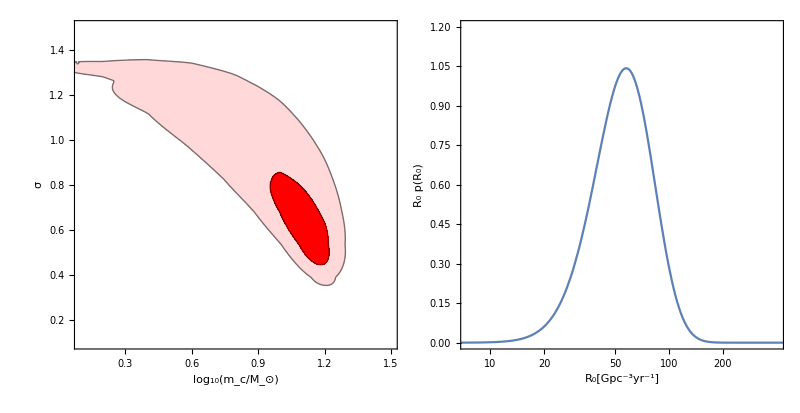

../latex/posterior-log.pdf

```mathematica
GraphicsGrid[{{p3,p2}},ImageSize->800,Spacings->Scaled[-.1]]
Export["../latex/posterior-log.pdf",%]
```